```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/sarp/Desktop/ACM_Modules_UCD/PHYC40900_TP_projects/2025_2026

## Exterior coordinate transformation

Here R is r̄ of the hand-written notes. OVerbar is written by highlighting the variable (in this case r) then hitting Ctrl+7

### Choosing: ∫R^-1 ⅆR = log[2R/M] yields R → r as r → ∞

```mathematica
rSol=r/.Solve[Log[2R/(M)]==2 ArcTanh[√(1-(2 M)/r)],r][[1]]//Simplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

2 M Cosh[1/2 Log[(2 R)/M]]^2

Sometimes Simplify isn’t “good enough”. So try FullSimplify

```mathematica
Simplify[rSol]
FullSimplify[rSol]
```

2 M Cosh[1/2 Log[(2 R)/M]]^2

M+M^2/(4 R)+R

% is the symbol for the most recent output, in this case  M+M^2/(4 R)+R, %% is the on before it. You can also use numbers like %2, %3 but the numbering follows a different rule (evaluations since you started a Kernel)

We get two solutions, pick the correct one by looking at the Limit of R/r at infinity

```mathematica
Rsol=Solve[r==%,R]
```

{{R→1/2 (-M+r-√(-2 M r+r^2))},{R→1/2 (-M+r+√(-2 M r+r^2))}}

```mathematica
Limit[(R/.Rsol[[1,1]])/r,r->Infinity]
Limit[(R/.Rsol[[2,1]])/r,r->Infinity]
```

0

1

Fractions are written by using Ctrl+/ after highlighting the numerator

### Some operations to help/check handwritten identities

```mathematica
D[Tanh[x]^2,x]//FunctionExpand
```

2 Sech[x]^2 Tanh[x]

```mathematica
FunctionExpand[Tanh[Log[u]]]
```

(-1+u^2)/(1+u^2)

```mathematica
Simplify[%/.u->(k r)/(1+√(1-k^2 r^2)),k>0]
```

-(1-k^2 r^2+√(1-k^2 r^2))/(1+√(1-k^2 r^2))

```mathematica
FullSimplify[%,k<1/r&&k>0]
```

-√(1-k^2 r^2)

```mathematica
Simplify[Tanh[Log[x]]]
```

(-1+x^2)/(1+x^2)

```mathematica
Simplify[Tanh[Log[√(2R/(M))]]]
```

-(M-2 R)/(M+2 R)

```mathematica
rSol2=Solve[(-α M+R)/(α M+R)==√(1-2 M/r),r][[1]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{r→(R^2+2 M R α+M^2 α^2)/(2 R α)}

### Obtain α=1/2

```mathematica
r/.rSol2
Rsol2=Solve[%==r,R]
αSol=Simplify[Limit[(R/.Rsol2)/r,r->Infinity],α>0]
Solve[αSol[[2]]==1,α]
```

(R^2+2 M R α+M^2 α^2)/(2 R α)

{{R→-M α+r α-√(-2 M r α^2+r^2 α^2)},{R→-M α+r α+√(-2 M r α^2+r^2 α^2)}}

{0,2 α}

{{α→1/2}}

Greek letters by squeezing the spelling in between escapes, e.g.,  α is given by Esc + alpha + Esc or Esc + a + Esc (don’t type the plus signs)

## Evaluate radial infall to r=2M

## Isotropic coords.

```mathematica
(* Drop position in Sch. coords. *)
R0=20;
```

Convert r=20M and r=2M to isotropic coordinate rBar,  written as R when the argument of a function

```mathematica
rofRbar[R_]=Block[{M=1},(M^2+4 M R+4 R^2)/(4 R)];
rBarofr[r_]=Block[{M=1},1/2 (-M+r+√(-2 M r+r^2))];
Rbar0=rBarofr[R0];
rBarEH=rBarofr[2];
```

Check limits at Infty and horizon (r=2M)

```mathematica
Limit[rBarofr[r]/r,r->Infinity]
rBarofr[2]
```

1

1/2

### Metric functions in isotropic coordinates

```mathematica
A[R_]=Block[{M=1},(1+M/(2R))^2];
α[R_]=Block[{M=1},(1-M/(2R))/(1+M/(2R))];
```

At r=R0 <---> r̄= R̄0 we have ur = 0 (the drop problem). I have {x,x’} ODEs, ie. \dot{x}=ODE1, \ddot{x} = ODE2, specifically {\dot{r̄}, \dot{ur}} system

Check that the energy is between 0 and 1 (bound)  and get the components of the 4-velocity at the initial drop point

```mathematica
E0=α[Rbar0];
0<E0<=1
Ut0=E0/α[Rbar0]^2;
Utdrop[R_]=E0/α[R]^2;
Urdrop[R_]=-1/A[R] √(E0^2/α[R]^2-1);
```

True

## Radial drop the simple way: τ=∫ dτ = ∫ dτ/drdr = ∫1/u^rdr

### Proper times calculated in either coord. system should match!

Set delay := only evaluates something when it’s called. The Schwarzschild result is the analytical solution from the MTW textbook

```mathematica
tSch[R_,rf_]:=Block[{M=1},-1/(√(2M))NIntegrate[(√(1-2M/R))/(√(1/r-1/R))1/(1-2 M/r),{r,R,rf}]];
τSch[R_,r_]=Block[{M=1},-1/(√(2M))(-r √(1/r-1/R) R-R^(3/2) ArcTan[√(1/r-1/R) √R])];
τIsotropic[r0_,r_]:=NIntegrate[1/Urdrop[R],{R,r0,r},WorkingPrecision->40]
```

```mathematica
NumericQ@τIsotropic[Rbar0,rBarEH]
Print["CHECK proper time equality: ",Abs[1-τSch[20,2]/τIsotropic[Rbar0,rBarEH]]<10^-16]
```

True

CHECK proper time equality: True

### Radial drop via NDSolving Eqs. (25a, 25b) of 2404.08735

```mathematica
Ut[R_,ur_]=1/α[R] √(1+ur^2/A[R]^2);
drBardt[R_,ur_]=1/(A[R]^2 Ut[R,ur])ur;
durdt[R_,ur_]=-α[R]Ut[R,ur]Derivative[1][α][R]+ur^2/Ut[R,ur](Derivative[1][A][R])/A[R]^3;
```

We set the start time to t0 = 0. The end time is tricky, if we pick something too large the ODE solver might get stuck trying to solve inside the black hole where we have no information at this point. So we use the analytical Sch. coordinate time t drop time to guide us. Note that t →∞  as r→2M so we pick rEnd=2.01, and r̄ accordingly.

```mathematica
t0=0;
rEnd=2.01;
rBarEnd=rBarofr[rEnd];
tEnd=tSch[R0,rEnd];
sol=NDSolve[{r'[t]==drBardt[r[t],ur[t]],ur'[t]==durdt[r[t],ur[t]],r[0]==Rbar0,ur[0]==0},{r,ur},{t,t0,tEnd}][[1]];
rNum=r/.sol;
urNum=ur/.sol;
```

Plot the solutions r(t) and ur(t)

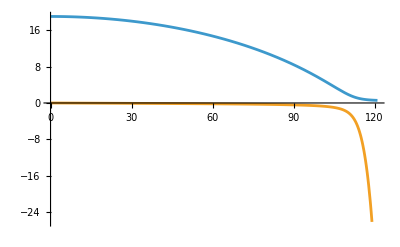

```mathematica
Plot[{rNum[t],urNum[t]},{t,t0,tEnd}]
```

### Check that the simple solution from ∫1/u^rdr and NDSolving the ODEs agree on the same r̄(τ) ↔ τ(r̄) as a function of the proper time

Use ParametricPlot here

```mathematica
τNDsolve[tf_]:=NIntegrate[α[rNum[t]]^2/E0,{t,t0,tf}];
```

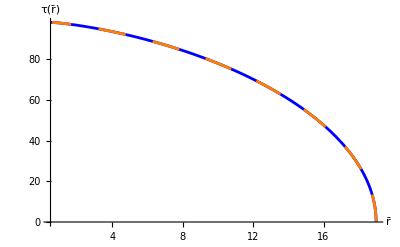

```mathematica
Show[Plot[τIsotropic[Rbar0,r],{r,Rbar0,rBarEH},PlotStyle->Blue]
,ParametricPlot[{rNum[tf],τNDsolve[tf]},{tf,t0,tEnd},PlotStyle->{Dashing[0.05],Orange}],AxesLabel->{"r̄","τ(r̄)"}]
```

## The constant density inner solution

## Set up the metric and the coord. transformation

Remember the mass sets the entire scale for the spacetime so easiest thing to do is setting it to one. Accordingly, we must pick a star radius which can be anything as long as it is greater than 2M (Sch. black hole radius). For a neutron star, R*=5M is reasonable.

```mathematica
Mst=1;
Rst=5;
```

### Interior solution functions

```mathematica
M[r_]=Piecewise[{{Mst r^3/Rst^3,r<=Rst},{Mst,r>Rst}}];
grrIn[r_]=(1-2 M[r]/r)^-1;
κ=√(2 Mst/Rst^3);
(* Integration constant *)
Cc=rBarofr[Rst] √((1+√(1-(2Mst)/Rst))/(1-√(1-2 Mst/Rst)));
rBarofrInside[r_]=Cc √((1-√(1-2 M[r]/r))/(1+√(1-2 M[r]/r)));
rofRbarInside[R_]=1/κ √(1-Tanh[Log[R/Cc]]^2);
```

Check that the inside/outside transformations agree on the surface

```mathematica
RbarSt=rBarofr[Rst];
RstVal==N[rofRbarInside[%]/.Mst->Mst/.Rst->Rst]
```

RstVal==5.

### Check that r->0 corresponds to r̄->0

```mathematica
0==Limit[rBarofrInside[r],r->0]
0==Limit[rofRbarInside[R],R->0]
0==Limit[FullSimplify[Series[rBarofrInside[r],{R,0,1}],0<r<Rst],r->0]
0==Limit[Simplify[Series[rofRbarInside[R],{R,0,1}],R>0],R->0]
```

True

True

True

«1 more identical outputs»

### Lapse and shift

```mathematica
αInside[R_]=(3/2 √(1-2 Mst/Rst)-1/2 √(1-2(Mst r^2)/Rst^3))/.r->rofRbarInside[R];
Ainside[R_]=rofRbarInside[R]/R;
(* CHECK that the spacetime is regular at R= 0 *)
αLim0=Limit[Simplify[Series[Ainside[R],{R,0,1}],R>0],R->0]//N
ALim0=Limit[Simplify[Series[αInside[R],{R,0,1}],R>0],R->0]//N
```

1.4315

0.661895

```mathematica
Show[Plot[Ainside[R],{R,0,3.9}]
,Plot[αInside[R],{R,0,3.9},PlotStyle->Orange]
,Graphics[{Blue,Disk[{0,αLim0},ImageScaled[{0.01,0.01}]]}]
,Graphics[{Red,Disk[{0,ALim0},ImageScaled[{0.01,0.01}]]}],PlotRange->All]
```

-Graphics-

### Construct the ODEs for the interior solution

```mathematica
UtInside[R_,ur_]=1/αInside[R] √(1+ur^2/Ainside[R]^2);
drBardtInside[R_,ur_]=1/(Ainside[R]^2 UtInside[R,ur])ur;
durdtInside[R_,ur_]=-αInside[R]UtInside[R,ur]Derivative[1][αInside][R]+ur^2/UtInside[R,ur](Derivative[1][Ainside][R])/Ainside[R]^3;
```

## Solve the ODEs for the infalling ``leg’’

The solver bails at r=0+ϵ, ϵ<<1

```mathematica
t0=0;
tEnd=200;
solIn=NDSolve[{r'[t]==Piecewise[{{drBardtInside[Abs[r[t]],ur[t]],r[t]<=RbarSt},{drBardt[Abs[r[t]],ur[t]],r[t]>RbarSt}}],ur'[t]==Piecewise[{{durdtInside[Abs[r[t]],ur[t]],r[t]<=RbarSt},{durdt[Abs[r[t]],ur[t]],r[t]>RbarSt}}],r[0]==Rbar0,ur[0]==0},{r,ur},{t,t0,tEnd}][[1]];
rNumIn=r/.solIn;
urNumIn=ur/.solIn;
```

NDSolve::ndsz: At t == 115.543, step size is effectively zero; singularity or stiff system suspected.

Get the time where the “crash” occurs

```mathematica
tCentralCrossing=rNumIn["Domain"][[1,2]]
(* Get the surface crossing time for plots *)
tSurface=t/.FindRoot[rNumIn[t]==RbarSt,{t,10,10,tCentralCrossing}]
```

115.543

104.013

## Plot the solution

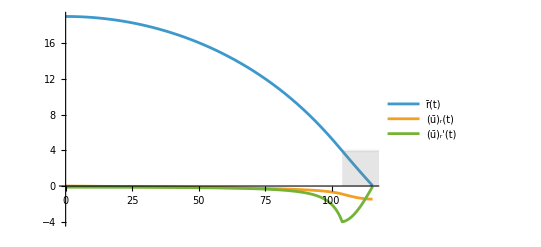

```mathematica
outFig=Show[Plot[{rNumIn[t],urNumIn[t],50urNumIn'[t]},{t,t0,.999tCentralCrossing},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]]
,Plot[RbarSt,{t,tSurface,tSurface+tCentralCrossing},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```